## Using EpidemicKabu to estimate the size of the COVID-19 epidemic waves

The estimations of the waves and measures of the waves size were made with the epidemic curve of an indicator of incident cases instead of just  the data of incident cases. The indicator the ratio between the cases of each date and the total population size by year multiplied per 100. We assume that the total population size of each country represent the susceptible population.

### Getting the data

```mathematica
data=Import["/Users/linaruiz/Documents/EpidemicKabu_project/EpidemicKabuLibrary/examples/data/wavesSizes.csv"];
Length@data
data[[;;10]]//Grid
data[[2;;,1]]//Union
data[[2;;,1]]//Union//Length
```

92

Country | waveNum | max | sum | spanDays | ratioSumSpan
Belgium | 0 | 0.0107959 | 0.527542 | 170 | 0.00310319
Belgium | 1 | 0.0997438 | 5.15165 | 199 | 0.0258877
Belgium | 2 | 0.035368 | 3.62333 | 169 | 0.0214398
Belgium | 3 | 0.132126 | 7.41145 | 173 | 0.0428407
Belgium | 4 | 0.316606 | 14.644 | 87 | 0.168322
Belgium | 5 | 0.0855082 | 4.3808 | 81 | 0.054084
Belgium | 6 | 0.0523065 | 2.93466 | 99 | 0.029643
Belgium | 7 | 0.0153611 | 0.316462 | 21 | 0.0150696
Bosnia and Herzegovina | 0 | 0.0011689 | 0.0534485 | 123 | 0.000434541

{Belgium,Bosnia and Herzegovina,Brazil,Colombia,Croatia,Ireland,Italy,Luxembourg,Norway,Republic of Korea,Romania,Spain,The United Kingdom,Türkiye,United States of America}

15

### Ordering the data

```mathematica
data2=Table[MapAt[{i,#}&,GroupBy[data[[2;;]],First][[i]],{All,3;;}],{i,1,15}];
data2[[;;2]]
```

{{{Belgium,0,{1,0.0107959},{1,0.527542},{1,170},{1,0.00310319}},{Belgium,1,{1,0.0997438},{1,5.15165},{1,199},{1,0.0258877}},{Belgium,2,{1,0.035368},{1,3.62333},{1,169},{1,0.0214398}},{Belgium,3,{1,0.132126},{1,7.41145},{1,173},{1,0.0428407}},{Belgium,4,{1,0.316606},{1,14.644},{1,87},{1,0.168322}},{Belgium,5,{1,0.0855082},{1,4.3808},{1,81},{1,0.054084}},{Belgium,6,{1,0.0523065},{1,2.93466},{1,99},{1,0.029643}},{Belgium,7,{1,0.0153611},{1,0.316462},{1,21},{1,0.0150696}}},{{Bosnia and Herzegovina,0,{2,0.0011689},{2,0.0534485},{2,123},{2,0.000434541}},{Bosnia and Herzegovina,1,{2,0.0365759},{2,3.55836},{2,266},{2,0.0133773}},{Bosnia and Herzegovina,2,{2,0.0370349},{2,2.60634},{2,157},{2,0.0166009}},{Bosnia and Herzegovina,3,{2,0.0209914},{2,1.89189},{2,141},{2,0.0134176}},{Bosnia and Herzegovina,4,{2,0.0494252},{2,3.41782},{2,184},{2,0.0185751}},{Bosnia and Herzegovina,5,{2,0.00978714},{2,0.650881},{2,128},{2,0.005085}}}}

```mathematica
Select[data2,StringContainsQ[#[[1,1]],"Croatia"]&]
```

{{{Croatia,0,{5,0.00143939},{5,0.0547028},{5,148},{5,0.000369614}},{Croatia,1,{5,0.00614144},{5,0.276461},{5,109},{5,0.00253634}},{Croatia,2,{5,0.080625},{5,5.4654},{5,152},{5,0.0359566}},{Croatia,3,{5,0.05012},{5,3.02184},{5,137},{5,0.0220572}},{Croatia,4,{5,0.118223},{5,7.35489},{5,167},{5,0.0440412}},{Croatia,5,{5,0.195785},{5,11.8733},{5,171},{5,0.0694344}},{Croatia,6,{5,0.0315822},{5,2.27655},{5,115},{5,0.0197961}}}}

```mathematica
Select[data2,StringContainsQ[#[[1,1]],"Italy"]&]
```

{{{Italy,0,{7,0.00652017},{7,0.405651},{7,185},{7,0.00219271}},{Italy,1,{7,0.0460495},{7,3.76802},{7,206},{7,0.0182913}},{Italy,2,{7,0.0333955},{7,2.9953},{7,150},{7,0.0199687}},{Italy,3,{7,0.00985211},{7,0.705376},{7,99},{7,0.00712501}},{Italy,4,{7,0.227824},{7,21.3037},{7,235},{7,0.090654}},{Italy,5,{7,0.122829},{7,8.57459},{7,124},{7,0.0691499}}}}

```mathematica
Select[data2,StringContainsQ[#[[1,1]],"Luxem"]&]
```

{{{Luxembourg,0,{8,0.0111665},{8,0.504484},{8,145},{8,0.0034792}},{Luxembourg,1,{8,0.00937485},{8,0.453211},{8,82},{8,0.00552697}},{Luxembourg,2,{8,0.086608},{8,7.10284},{8,170},{8,0.0417814}},{Luxembourg,3,{8,0.0319201},{8,3.05956},{8,133},{8,0.0230042}},{Luxembourg,4,{8,0.0131414},{8,0.66708},{8,61},{8,0.0109357}},{Luxembourg,5,{8,0.248864},{8,26.635},{8,283},{8,0.0941166}},{Luxembourg,6,{8,0.099833},{8,6.49364},{8,114},{8,0.0569617}},{Luxembourg,7,{8,0.0218511},{8,0.232519},{8,11},{8,0.0211381}}}}

```mathematica
Select[data2,StringContainsQ[#[[1,1]],"Norw"]&]
```

{{{Norway,0,{9,0.00201503},{9,0.164671},{9,174},{9,0.000946385}},{Norway,1,{9,0.0115255},{9,2.21516},{9,359},{9,0.00617035}},{Norway,2,{9,0.234575},{9,24.5763},{9,466},{9,0.0527389}}}}

```mathematica
Select[data2,StringContainsQ[#[[1,1]],"Rep"]&]
```

{{{Republic of Korea,0,{10,0.000333231},{10,0.0223858},{10,143},{10,0.000156544}},{Republic of Korea,1,{10,0.00136445},{10,0.151262},{10,280},{10,0.000540223}},{Republic of Korea,2,{10,0.454465},{10,35.0655},{10,472},{10,0.0742914}},{Republic of Korea,3,{10,0.170172},{10,12.6344},{10,104},{10,0.121485}}}}

```mathematica
Select[data2,StringContainsQ[#[[1,1]],"Kin"]&]
```

{{{The United Kingdom,0,{13,0.00641652},{13,0.433809},{13,192},{13,0.00225942}},{The United Kingdom,1,{13,0.067364},{13,6.2619},{13,292},{13,0.0214449}},{The United Kingdom,2,{13,0.0503817},{13,2.39076},{13,97},{13,0.0246471}},{The United Kingdom,3,{13,0.211633},{13,19.1729},{13,207},{13,0.0926226}},{The United Kingdom,4,{13,0.100733},{13,4.7894},{13,85},{13,0.0563458}},{The United Kingdom,5,{13,0.0316702},{13,2.02752},{13,126},{13,0.0160915}}}}

### Plot1

For all the waves of each country  is made a ListPlot of the “Total number of cases/totalPop*100”,  “Maximum number of cases/totalPop*100”, “Maximum number of cases/totalPop*100 normalized”

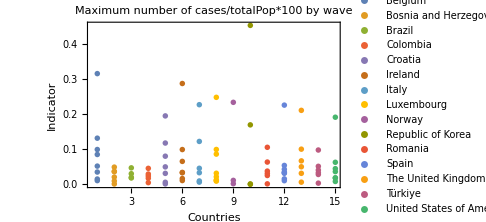
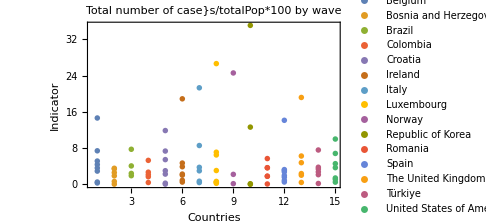
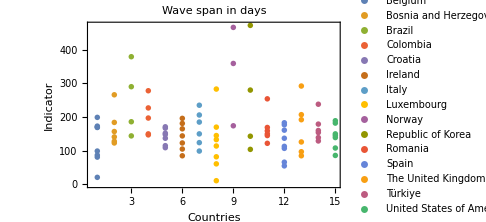
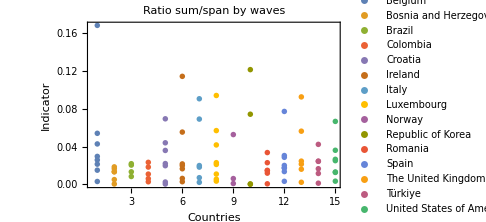

```mathematica
listPlot=ListPlot[#[[1]],PlotLabel->#[[2]],PlotRange->All,ImageSize->Medium,Frame->True,FrameLabel->{"Countries","Indicator"},PlotLegends->data2[[All,1,1]]]&/@{
{data2[[All,All,3]],"Maximum number of cases/totalPop*100 by wave"},
{data2[[All,All,4]],"Total number of case}s/totalPop*100 by wave"},
{data2[[All,All,5]],"Wave span in days"},
{data2[[All,All,6]],"Ratio sum/span by waves"}}
```

### Plot2

For all the waves of each country  is made a BoxWhiskerChart of the “Total number of cases/totalPop*100”,  “Maximum number of cases/totalPop*100”, “Maximum number of cases/totalPop*100 normalized”

{Belgium,Bosnia and Herzegovina,Brazil,Colombia,Croatia,Ireland,Italy,Luxembourg,Norway,Republic of Korea,Romania,Spain,The United Kingdom,Türkiye,United States of America}

Maximum number of cases/totalPop*100 by wave

Total number of cases/totalPop*100 by wave

Wave span in days

Ratio sum/span by waves

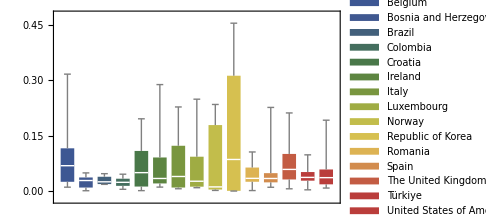
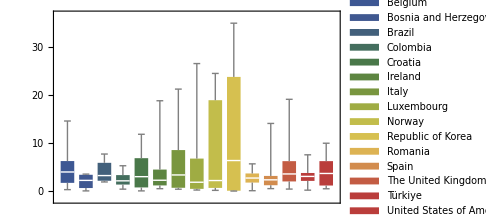
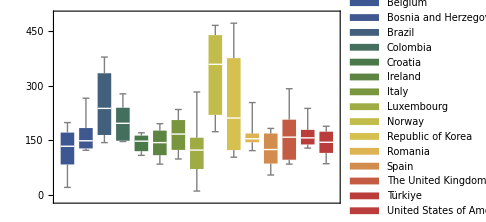
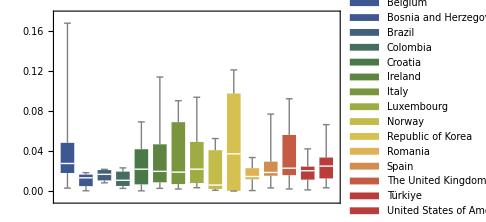

```mathematica
data3=GroupBy[data,First];
boxPlot=BoxWhiskerChart[#[[1]],ChartLabels->Echo[#[[2]]],ChartLegends->(data3[[2;;,1]]//Keys), ChartStyle->"DarkRainbow",ImageSize->Medium,FrameTicksStyle->Directive[Black,12]]&/@{
{data3[[2;;,All,3]],"Maximum number of cases/totalPop*100 by wave"},
{data3[[2;;,All,4]],"Total number of cases/totalPop*100 by wave"},
{data3[[2;;,All,5]],"Wave span in days"},
{data3[[2;;,All,6]],"Ratio sum/span by waves"}}
```

```mathematica
zz
```

### Plot 3

Merging the ListPlot and BoxWhiskerChart

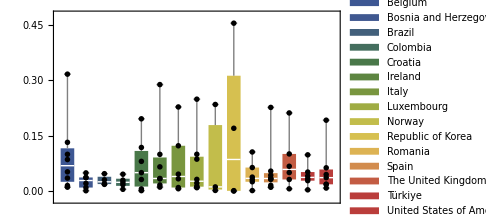
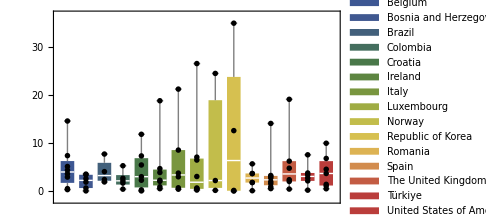
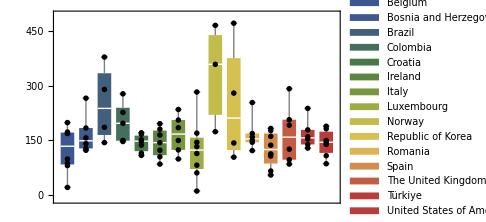
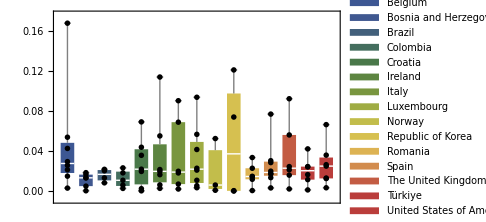

```mathematica
listPlot2=ListPlot[#[[1]],PlotLabel->#[[2]],PlotRange->All,ImageSize->Medium,Frame->True,FrameLabel->{"Countries","Indicator"},PlotStyle->Black]&/@{{data2[[All,All,3]],"Maximum number of cases/totalPop*100 by wave"},
{data2[[All,All,4]],"Total number of cases/totalPop*100 by wave"},
{data2[[All,All,5]],"Wave span in days"},
{data2[[All,All,6]],"Ratio sum/span by waves"}};
(*This listPlot2 is the same as listPlot2 but without Legends*)

Show[boxPlot[[#]],listPlot2[[#]]]&/@{1,2,3,4}
```

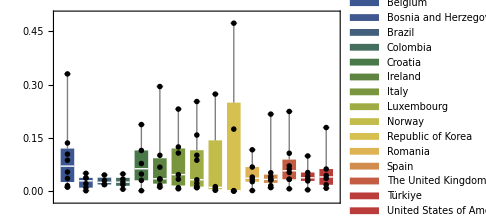
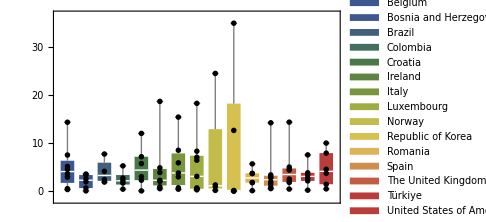
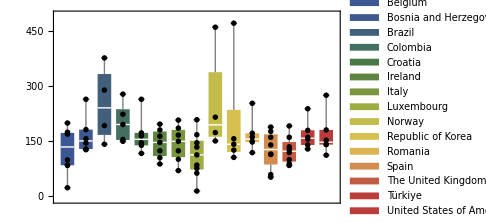
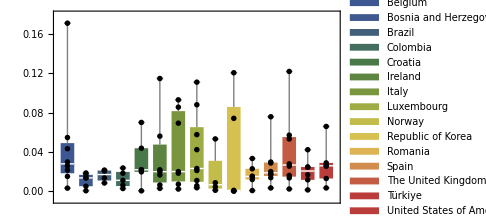

### Plot 4

Plotting the Total number of cases/totalPop*100”|”Maximum number of cases/totalPop*100”|”Maximum number of cases/totalPop*100 normalized”  values of for all the waves of all countries in a unique BoxWhiskerChart and repeating this plot as many countries there are

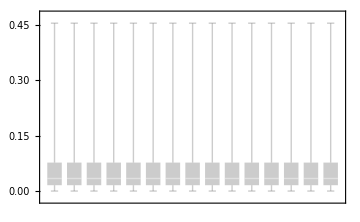
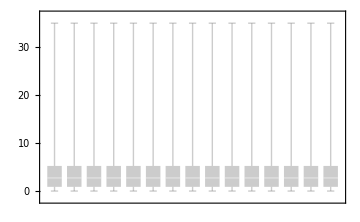
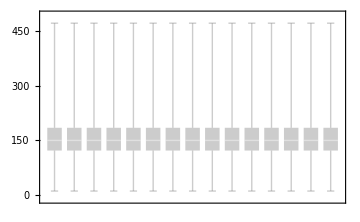
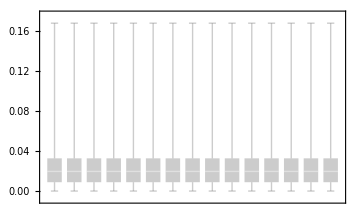

```mathematica
allBoxPlot=BoxWhiskerChart[Table[Flatten@GatherBy[data[[2;;]],First][[All,All,#[[1]]]],Length[data2[[All,1,1]]]],ImageSize->Medium,ChartStyle->Opacity[0.4,Gray],FrameTicksStyle->Directive[Black,12]]&/@{
{3,"Maximum number of cases/totalPop*100 by wave"},
{4,"Total number of cases/totalPop*100 by wave"},
{5,"Wave span in days"},
{6,"Ratio sum/span by waves"}}
```

### Plot 5

Plotting the Total number of cases/totalPop*100”|”Maximum number of cases/totalPop*100”|”Maximum number of cases/totalPop*100 normalized”  values of for all the waves of all countries in a unique BoxWhiskerChart and repeating this plot as many countries there are, and adding the points of the values belonging to each country

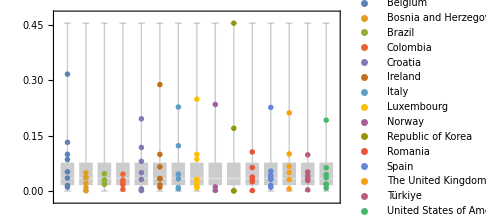
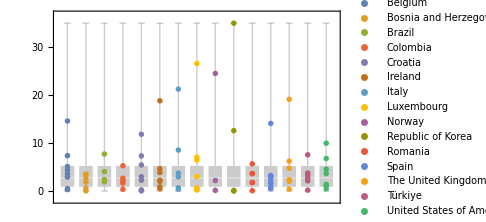
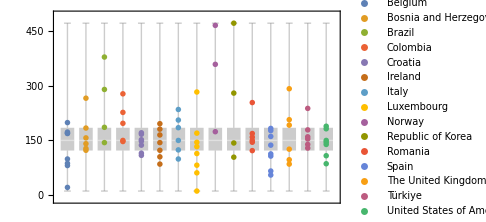
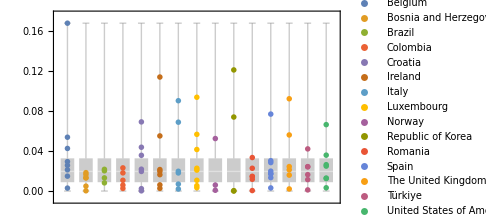

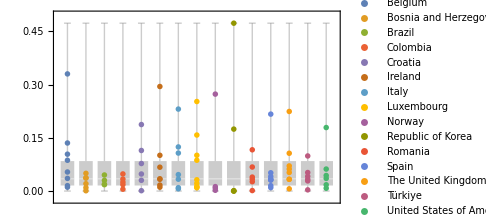
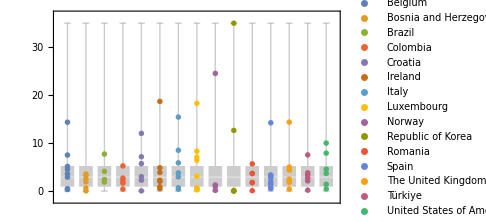
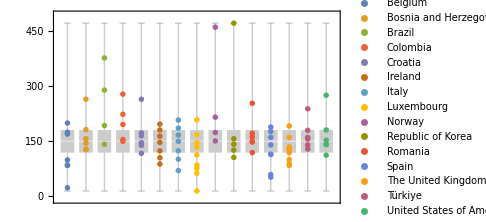
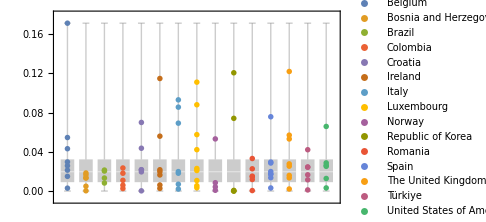

```mathematica
Show[allBoxPlot[[#]],listPlot[[#]]]&/@{1,2,3,4}
```

```mathematica
14/200.
```

0.07

### Summary of the estimations for each country

```mathematica
countries=data[[2;;,1]]//DeleteDuplicates
```

{Belgium,Bosnia and Herzegovina,Brazil,Colombia,Croatia,Ireland,Italy,Luxembourg,Norway,Republic of Korea,Romania,Spain,The United Kingdom,Türkiye,United States of America}

#### Maximum value

Getting some basic descriptions

```mathematica
descriptions={
#[[1]],
Min[#[[2]]],
Max[#[[2]]],
Mean[#[[2]]],
StandardDeviation[#[[2]]],
Variance[#[[2]]]
}&/@Thread[countries->GatherBy[data[[2;;]],First][[All,All,3]]]
```

{{Belgium,0.0107959,0.316606,0.093477,0.0995656,0.00991331},{Bosnia and Herzegovina,0.0011689,0.0494252,0.0258306,0.0183669,0.000337343},{Brazil,0.0184182,0.0473232,0.0290863,0.0133123,0.000177219},{Colombia,0.00505022,0.045901,0.0244028,0.0150973,0.000227929},{Croatia,0.00143939,0.195785,0.0691308,0.0694076,0.00481742},{Ireland,0.0109901,0.288356,0.0784557,0.0974699,0.00950037},{Italy,0.00652017,0.227824,0.0744118,0.08619,0.00742871},{Luxembourg,0.00937485,0.248864,0.0653449,0.0820478,0.00673184},{Norway,0.00201503,0.234575,0.0827053,0.131609,0.017321},{Republic of Korea,0.000333231,0.454465,0.156584,0.214029,0.0458083},{Romania,0.00162888,0.106047,0.0443865,0.0362819,0.00131637},{Spain,0.0105523,0.226597,0.0563663,0.0701764,0.00492473},{The United Kingdom,0.00641652,0.211633,0.0780331,0.0728301,0.00530422},{Türkiye,0.00361621,0.0982748,0.0427418,0.031593,0.000998118},{United States of America,0.00843926,0.192028,0.0546319,0.0633809,0.00401714}}

Countries with the lowest Maximum value by wave

```mathematica
Select[descriptions,#[[2]]==Min[descriptions[[All,2]]]&][[All,{1,2}]]
```

{{Republic of Korea,0.000333231}}

Countries with the highest Maximum value by wave

```mathematica
Select[descriptions,#[[3]]==Max[descriptions[[All,3]]]&][[All,{1,3}]]
```

{{Republic of Korea,0.454465}}

Countries with the lowest mean of  the maximum values of their set of waves

```mathematica
Select[descriptions,#[[4]]==Min[descriptions[[All,4]]]&][[All,{1,4}]]
```

{{Colombia,0.0244028}}

Countries with the highest mean of  the maximum values of their set of waves

```mathematica
Select[descriptions,#[[4]]==Max[descriptions[[All,4]]]&][[All,{1,4}]]
```

{{Republic of Korea,0.156584}}

Countries with the lowest sd of  the maximum values of their set of waves

```mathematica
Select[descriptions,#[[5]]==Min[descriptions[[All,5]]]&][[All,{1,5}]]
```

{{Brazil,0.0133123}}

Countries with the highest sd of  the maximum values of their set of waves

```mathematica
Select[descriptions,#[[5]]==Max[descriptions[[All,5]]]&][[All,{1,5}]]
```

{{Republic of Korea,0.214029}}

Countries with the lowest variance of  the maximum values of their set of waves

```mathematica
Select[descriptions,#[[6]]==Min[descriptions[[All,6]]]&][[All,{1,6}]]
```

{{Brazil,0.000177219}}

Countries with the highest variance of  the maximum values of their set of waves

```mathematica
Select[descriptions,#[[6]]==Max[descriptions[[All,6]]]&][[All,{1,6}]]
```

{{Republic of Korea,0.0458083}}

#### Total

Getting some basic descriptions

```mathematica
descriptionsT={
#[[1]],
Min[#[[2]]],
Max[#[[2]]],
Mean[#[[2]]],
StandardDeviation[#[[2]]],
Variance[#[[2]]]
}&/@Thread[countries->GatherBy[data[[2;;]],First][[All,All,4]]];
```

Countries with the lowest Total by wave

```mathematica
Select[descriptionsT,#[[2]]==Min[descriptionsT[[All,2]]]&][[All,{1,2}]]
```

{{Republic of Korea,0.0223858}}

Countries with the highest Total by wave

```mathematica
Select[descriptionsT,#[[3]]==Max[descriptionsT[[All,3]]]&][[All,{1,3}]]
```

{{Republic of Korea,35.0655}}

Countries with the lowest mean of  the totals of their set of waves

```mathematica
Select[descriptionsT,#[[4]]==Min[descriptionsT[[All,4]]]&][[All,{1,4}]]
```

{{Bosnia and Herzegovina,2.02979}}

Countries with the highest mean of  the totals of their set of waves

```mathematica
Select[descriptionsT,#[[4]]==Max[descriptionsT[[All,4]]]&][[All,{1,4}]]
```

{{Republic of Korea,11.9684}}

Countries with the lowest sd of  the totals of their set of waves

```mathematica
Select[descriptionsT,#[[5]]==Min[descriptionsT[[All,5]]]&][[All,{1,5}]]
```

{{Bosnia and Herzegovina,1.44374}}

Countries with the highest sd of  the totals of their set of waves

```mathematica
Select[descriptionsT,#[[5]]==Max[descriptionsT[[All,5]]]&][[All,{1,5}]]
```

{{Republic of Korea,16.4952}}

Countries with the lowest variance of  the totals of their set of waves

```mathematica
Select[descriptionsT,#[[6]]==Min[descriptionsT[[All,6]]]&][[All,{1,6}]]
```

{{Bosnia and Herzegovina,2.08438}}

Countries with the highest variance of  the totals of their set of waves

```mathematica
Select[descriptionsT,#[[6]]==Max[descriptionsT[[All,6]]]&][[All,{1,6}]]
```

{{Republic of Korea,272.091}}

#### Duration in days

Getting some basic descriptions

```mathematica
descriptionsD={
#[[1]],
Min[#[[2]]],
Max[#[[2]]],
Mean[#[[2]]],
StandardDeviation[#[[2]]],
Variance[#[[2]]]
}&/@Thread[countries->GatherBy[data[[2;;]],First][[All,All,5]]];
```

Countries with the lowest Duration in days by wave

```mathematica
Select[descriptionsD,#[[2]]==Min[descriptionsD[[All,2]]]&][[All,{1,2}]]
```

{{Luxembourg,11}}

Countries with the highest Duration in days by wave

```mathematica
Select[descriptionsD,#[[3]]==Max[descriptionsD[[All,3]]]&][[All,{1,3}]]
```

{{Republic of Korea,472}}

Countries with the lowest mean of  the Duration in days of their set of waves

```mathematica
N@Select[descriptionsD,#[[4]]==Min[descriptionsD[[All,4]]]&][[All,{1,4}]]
```

{{Belgium,124.875},{Luxembourg,124.875},{Spain,124.875}}

Countries with the highest mean of  the Duration in days of their set of waves

```mathematica
N@Select[descriptionsD,#[[4]]==Max[descriptionsD[[All,4]]]&][[All,{1,4}]]
```

{{Norway,333.}}

{{Brazil,249.75},{Norway,249.75}}

Countries with the lowest sd of  the Duration in days of their set of waves

```mathematica
N@Select[descriptionsD,#[[5]]==Min[descriptionsD[[All,5]]]&][[All,{1,5}]]
```

{{The United Kingdom,36.8799}}

Countries with the highest sd of  the Duration in days of their set of waves

```mathematica
N@Select[descriptionsD,#[[5]]==Max[descriptionsD[[All,5]]]&][[All,{1,5}]]
```

{{Republic of Korea,166.282}}

{{Republic of Korea,153.339}}

#### Ratio

Getting some basic descriptions

```mathematica
descriptionsR={
#[[1]],
Min[#[[2]]],
Max[#[[2]]],
Mean[#[[2]]],
StandardDeviation[#[[2]]],
Variance[#[[2]]]
}&/@Thread[countries->GatherBy[data[[2;;]],First][[All,All,6]]];
```

Countries with the lowest Ratio by wave

```mathematica
Select[descriptionsR,#[[2]]==Min[descriptionsR[[All,2]]]&][[All,{1,2}]]
```

{{Republic of Korea,0.000156544}}

Countries with the highest Ratio  by wave

```mathematica
Select[descriptionsR,#[[3]]==Max[descriptionsR[[All,3]]]&][[All,{1,3}]]
```

{{Belgium,0.168322}}

Countries with the lowest mean of  the ratio  of their set of waves

```mathematica
Select[descriptionsR,#[[4]]==Min[descriptionsR[[All,4]]]&][[All,{1,4}]]
```

{{Bosnia and Herzegovina,0.0112484}}

Countries with the highest mean of  the ratios  of their set of waves

```mathematica
Select[descriptionsR,#[[4]]==Max[descriptionsR[[All,4]]]&][[All,{1,4}]]
```

{{Republic of Korea,0.0491183}}

Countries with the lowest sd of  the ratios of their set of waves

```mathematica
Select[descriptionsR,#[[5]]==Min[descriptionsR[[All,5]]]&][[All,{1,5}]]
```

{{Brazil,0.00633102}}

Countries with the highest sd of  the ratios of their set of waves

```mathematica
Select[descriptionsR,#[[5]]==Max[descriptionsR[[All,5]]]&][[All,{1,5}]]
```

{{Republic of Korea,0.0595194}}

### Summary of the estimations for all the countries at once

```mathematica
countries=data[[2;;,1]]//DeleteDuplicates
```

{Belgium,Bosnia and Herzegovina,Brazil,Colombia,Croatia,Ireland,Italy,Luxembourg,Norway,Republic of Korea,Romania,Spain,The United Kingdom,Türkiye,United States of America}

#### Maximum value

Getting some basic descriptions

```mathematica
descriptions={
Min[#],
Max[#],
Mean[#],
StandardDeviation[#]
}&@Flatten@GatherBy[data[[2;;]],First][[All,All,3]]
```

{0.000333231,0.454465,0.0642007,0.0806066}

#### Total

Getting some basic descriptions

```mathematica
descriptions={
Min[#],
Max[#],
Mean[#],
StandardDeviation[#]
}&@Flatten@GatherBy[data[[2;;]],First][[All,All,4]]
```

{0.0223858,35.0655,4.7133,6.24178}

#### Duration in days

Getting some basic descriptions

```mathematica
descriptions=N@{
Min[#],
Max[#],
Mean[#],
StandardDeviation[#]
}&@Flatten@GatherBy[data[[2;;]],First][[All,All,5]]
```

{11.,472.,164.67,78.7}

#### Ratio

Getting some basic descriptions

```mathematica
descriptions={
Min[#],
Max[#],
Mean[#],
StandardDeviation[#]
}&@Flatten@GatherBy[data[[2;;]],First][[All,All,6]]
```

{0.000156544,0.168322,0.0278083,0.0300781}

### ytf

```mathematica
GatherBy[data[[2;;]],First][[All,All,All]]
```

{{{Belgium,0,0.0107959,0.527542,170,0.00310319},{Belgium,1,0.0997438,5.15165,199,0.0258877},{Belgium,2,0.035368,3.62333,169,0.0214398},{Belgium,3,0.132126,7.41145,173,0.0428407},{Belgium,4,0.316606,14.644,87,0.168322},{Belgium,5,0.0855082,4.3808,81,0.054084},{Belgium,6,0.0523065,2.93466,99,0.029643},{Belgium,7,0.0153611,0.316462,21,0.0150696}},{{Bosnia and Herzegovina,0,0.0011689,0.0534485,123,0.000434541},{Bosnia and Herzegovina,1,0.0365759,3.55836,266,0.0133773},{Bosnia and Herzegovina,2,0.0370349,2.60634,157,0.0166009},{Bosnia and Herzegovina,3,0.0209914,1.89189,141,0.0134176},{Bosnia and Herzegovina,4,0.0494252,3.41782,184,0.0185751},{Bosnia and Herzegovina,5,0.00978714,0.650881,128,0.005085}},{{Brazil,0,0.0184182,2.42664,290,0.00836771},{Brazil,1,0.0306226,7.7481,379,0.0204435},{Brazil,2,0.0473232,4.07823,186,0.021926},{Brazil,3,0.0199813,1.91942,144,0.0133293}},{{Colombia,0,0.0175072,1.69563,278,0.00609938},{Colombia,1,0.0239329,2.69836,147,0.0183562},{Colombia,2,0.045901,5.30303,227,0.0233614},{Colombia,3,0.0296228,2.15324,197,0.0109302},{Colombia,4,0.00505022,0.417531,150,0.00278354}},{{Croatia,0,0.00143939,0.0547028,148,0.000369614},{Croatia,1,0.00614144,0.276461,109,0.00253634},{Croatia,2,0.080625,5.4654,152,0.0359566},{Croatia,3,0.05012,3.02184,137,0.0220572},{Croatia,4,0.118223,7.35489,167,0.0440412},{Croatia,5,0.195785,11.8733,171,0.0694344},{Croatia,6,0.0315822,2.27655,115,0.0197961}},{{Ireland,0,0.0109901,0.51513,181,0.00284602},{Ireland,1,0.0167985,0.913262,144,0.0063421},{Ireland,2,0.0657936,3.89649,196,0.01988},{Ireland,3,0.0333085,2.27852,105,0.0217001},{Ireland,4,0.288356,18.873,165,0.114382},{Ireland,5,0.099593,4.70768,85,0.0553844},{Ireland,6,0.0343496,2.03676,123,0.016559}},{{Italy,0,0.00652017,0.405651,185,0.00219271},{Italy,1,0.0460495,3.76802,206,0.0182913},{Italy,2,0.0333955,2.9953,150,0.0199687},{Italy,3,0.00985211,0.705376,99,0.00712501},{Italy,4,0.227824,21.3037,235,0.090654},{Italy,5,0.122829,8.57459,124,0.0691499}},{{Luxembourg,0,0.0111665,0.504484,145,0.0034792},{Luxembourg,1,0.00937485,0.453211,82,0.00552697},{Luxembourg,2,0.086608,7.10284,170,0.0417814},{Luxembourg,3,0.0319201,3.05956,133,0.0230042},{Luxembourg,4,0.0131414,0.66708,61,0.0109357},{Luxembourg,5,0.248864,26.635,283,0.0941166},{Luxembourg,6,0.099833,6.49364,114,0.0569617},{Luxembourg,7,0.0218511,0.232519,11,0.0211381}},{{Norway,0,0.00201503,0.164671,174,0.000946385},{Norway,1,0.0115255,2.21516,359,0.00617035},{Norway,2,0.234575,24.5763,466,0.0527389}},{{Republic of Korea,0,0.000333231,0.0223858,143,0.000156544},{Republic of Korea,1,0.00136445,0.151262,280,0.000540223},{Republic of Korea,2,0.454465,35.0655,472,0.0742914},{Republic of Korea,3,0.170172,12.6344,104,0.121485}},{{Romania,0,0.00162888,0.093303,145,0.000643469},{Romania,1,0.0380463,3.69183,254,0.0145348},{Romania,2,0.0254391,1.78812,150,0.0119208},{Romania,3,0.0638884,3.65514,159,0.0229883},{Romania,4,0.106047,5.69812,169,0.0337167},{Romania,5,0.0312691,1.81972,122,0.0149157}},{{Spain,0,0.0105523,0.527586,161,0.00327693},{Spain,1,0.0355227,3.08532,177,0.0174312},{Spain,2,0.0542418,3.26985,107,0.0305593},{Spain,3,0.0158591,0.896395,66,0.0135817},{Spain,4,0.0432191,2.75194,137,0.0200872},{Spain,5,0.226597,14.1359,183,0.0772455},{Spain,6,0.0318301,1.5766,55,0.0286654},{Spain,7,0.0331083,1.97299,113,0.0174601}},{{The United Kingdom,0,0.00641652,0.433809,192,0.00225942},{The United Kingdom,1,0.067364,6.2619,292,0.0214449},{The United Kingdom,2,0.0503817,2.39076,97,0.0246471},{The United Kingdom,3,0.211633,19.1729,207,0.0926226},{The United Kingdom,4,0.100733,4.7894,85,0.0563458},{The United Kingdom,5,0.0316702,2.02752,126,0.0160915}},{{Türkiye,0,0.00361621,0.206504,160,0.00129065},{Türkiye,1,0.0283905,2.75876,238,0.0115914},{Türkiye,2,0.051719,3.39323,139,0.0244118},{Türkiye,3,0.0334536,3.79251,154,0.0246267},{Türkiye,4,0.0982748,7.58733,179,0.0423873},{Türkiye,5,0.0409968,2.14175,129,0.0166027}},{{United States of America,0,0.00843926,0.497325,145,0.00342983},{United States of America,1,0.0184432,1.42065,108,0.0131542},{United States of America,2,0.0632109,6.82776,189,0.0361257},{United States of America,3,0.0187251,1.09163,86,0.0126934},{United States of America,4,0.0450024,3.69191,139,0.0265605},{United States of America,5,0.192028,10.0044,150,0.0666959},{United States of America,6,0.0365742,4.57433,182,0.0251337}}}

```mathematica
SortBy[#,Last]&@Flatten[#,1]&@GatherBy[data[[2;;]],First][[All,All,All]]
```

{{Republic of Korea,0,0.000352074,0.0221261,141,0.000156923},{Republic of Korea,1,0.000321497,0.0221848,125,0.000177478},{Croatia,0,0.00133117,0.054485,145,0.000375758},{Bosnia and Herzegovina,0,0.0011789,0.0566137,126,0.000449315},{Romania,0,0.00168982,0.0954426,147,0.000649269},{Republic of Korea,2,0.00140429,0.128329,156,0.000822621},{Norway,0,0.00248778,0.162723,173,0.000940598},{Türkiye,0,0.00367849,0.206477,160,0.00129048},{Italy,0,0.00661258,0.405639,185,0.00219265},{The United Kingdom,0,0.00661976,0.432786,191,0.0022659},{Colombia,4,0.00550584,0.418195,154,0.00271555},{Ireland,0,0.0112088,0.514849,180,0.00286027},{Belgium,0,0.0111486,0.527596,170,0.00310351},{Spain,0,0.00992989,0.526468,160,0.00329043},{United States of America,0,0.00827781,0.469194,141,0.00332761},{Luxembourg,0,0.0114512,0.504534,145,0.00347954},{Norway,1,0.00852052,0.946853,215,0.00440397},{Bosnia and Herzegovina,5,0.00990378,0.650117,128,0.00507904},{Luxembourg,1,0.00950689,0.467637,84,0.0055671},{Colombia,0,0.0183685,1.694,278,0.00609354},{Ireland,1,0.0171041,0.921178,146,0.00630944},{Italy,3,0.00991803,0.71149,100,0.0071149},{Brazil,0,0.018229,2.41404,289,0.00835309},{Norway,2,0.0127933,1.29546,150,0.00863637},{Luxembourg,4,0.0133203,0.674317,62,0.0108761},{Colombia,3,0.0339346,2.15699,195,0.0110615},{Türkiye,1,0.028792,2.75873,238,0.0115913},{Romania,2,0.0266035,1.77462,149,0.0119102},{United States of America,1,0.0179699,1.43674,111,0.0129436},{Brazil,3,0.0195026,1.8903,141,0.0134064},{Bosnia and Herzegovina,1,0.0369286,3.56575,264,0.0135066},{The United Kingdom,1,0.0334129,1.81581,134,0.0135508},{Bosnia and Herzegovina,3,0.0210718,1.95285,144,0.0135615},{Spain,3,0.0155218,0.797434,58,0.0137489},{Romania,1,0.0396329,3.70319,253,0.0146371},{Belgium,7,0.0155236,0.33246,22,0.0151118},{Romania,5,0.0337081,1.80743,118,0.0153172},{The United Kingdom,7,0.0334592,2.02748,126,0.0160911},{Ireland,6,0.0348242,2.03547,123,0.0165485},{Bosnia and Herzegovina,2,0.0374818,2.59585,156,0.0166401},{Türkiye,5,0.0417738,2.13845,128,0.0167066},{Spain,1,0.0344547,3.04108,176,0.0172789},{Spain,7,0.0318019,1.97462,113,0.0174746},{Colombia,1,0.025424,2.72477,149,0.018287},{Italy,1,0.0465836,3.791,207,0.018314},{Bosnia and Herzegovina,4,0.0501948,3.35687,181,0.0185463},{Croatia,5,0.0305444,2.2848,116,0.0196965},{Ireland,2,0.0674906,3.89662,196,0.0198807},{Italy,2,0.0336281,2.97226,149,0.019948},{Spain,4,0.041459,2.77989,139,0.0199992},{Brazil,1,0.0304503,7.7416,377,0.0205348},{Luxembourg,8,0.0219885,0.27403,13,0.0210793},{Belgium,2,0.0359951,3.62356,169,0.0214412},{Brazil,2,0.0455621,4.13048,192,0.0215129},{Croatia,1,0.0778543,5.74166,264,0.0217487},{Ireland,3,0.0335121,2.27121,104,0.0218385},{Croatia,2,0.048322,3.02465,138,0.0219177},{Romania,3,0.0679816,3.67165,161,0.0228053},{Luxembourg,3,0.0320642,3.07664,133,0.0231326},{Colombia,2,0.0484989,5.27128,223,0.023638},{Türkiye,2,0.0524771,3.39335,139,0.0244126},{Türkiye,3,0.0335337,3.82151,155,0.0246549},{United States of America,5,0.0358905,4.55907,180,0.0253282},{The United Kingdom,3,0.0526185,2.52363,99,0.0254912},{Belgium,1,0.104198,5.15112,199,0.025885},{United States of America,3,0.0440912,3.69775,140,0.0264125},{The United Kingdom,2,0.0710818,4.45072,160,0.027817},{Spain,6,0.0311552,1.46332,51,0.0286925},{United States of America,2,0.0622513,7.9263,275,0.0288229},{Spain,2,0.0517888,3.38209,114,0.0296674},{Belgium,6,0.0539906,2.91928,98,0.0297885},{Romania,4,0.116524,5.68983,171,0.0332739},{Türkiye,4,0.099165,7.56002,179,0.0422348},{Luxembourg,2,0.0871602,7.06386,167,0.0422986},{Belgium,3,0.135652,7.52842,174,0.0432668},{Croatia,3,0.114587,7.17545,164,0.0437527},{The United Kingdom,4,0.0622485,4.41654,83,0.0532113},{Norway,3,0.273392,24.5457,461,0.0532445},{Belgium,5,0.0870061,4.53648,83,0.0546563},{Ireland,5,0.101009,4.87416,87,0.0560248},{The United Kingdom,6,0.106747,5.02263,88,0.0570753},{Luxembourg,7,0.101047,6.45219,112,0.0576088},{United States of America,4,0.179187,10.0222,152,0.0659355},{Italy,6,0.124557,8.52152,123,0.0692806},{Croatia,4,0.187626,12.0424,172,0.0700142},{Republic of Korea,3,0.473144,35.0207,472,0.0741964},{Spain,5,0.217017,14.2524,188,0.0758105},{Italy,5,0.107337,5.90643,69,0.0856004},{Luxembourg,5,0.252525,18.307,208,0.0880146},{Italy,4,0.231211,15.4426,166,0.0930278},{Luxembourg,6,0.1581,8.32827,75,0.111044},{Ireland,4,0.294769,18.7071,163,0.114768},{Republic of Korea,4,0.174792,12.6624,105,0.120594},{The United Kingdom,5,0.224487,14.3864,118,0.121919},{Belgium,4,0.330276,14.3718,84,0.171093}}